```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True];
```

Successfully patched FeynArts.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
LoadModel["../Feyn/ALP_leptophilic"];
```

loading classes model file /home/jorge/Documents/GitHub/tauALPs/PseudoScalar/Feyn/ALP_leptophilic.mod

```mathematica
top = CreateTopologies[0, 2->3];
```

```mathematica
diag = InsertFields[top, {F[4], -F[3]}-> {S[105], F[2], -F[1]}, Model->"ALP_leptophilic", GenericModel->"ALP_leptophilic", InsertionLevel->{Classes}, ExcludeParticles->{S[2], S[3]}];
```

loading generic model file /home/jorge/.Mathematica/Applications/FeynArts/Models/ALP_leptophilic.gen

> $GenericMixing is OFF

generic model {ALP_leptophilic} initialized

loading classes model file /home/jorge/.Mathematica/Applications/FeynArts/Models/ALP_leptophilic.mod

> 44 particles (incl. antiparticles) in 17 classes

> $CounterTerms are ON

> 95 vertices

classes model {ALP_leptophilic} initialized

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 0 Classes insertions

> Top. 8: 0 Classes insertions

> Top. 9: 0 Classes insertions

> Top. 10: 0 Classes insertions

> Top. 11: 1 Classes insertion

> Top. 12: 0 Classes insertions

> Top. 13: 1 Classes insertion

> Top. 14: 0 Classes insertions

> Top. 15: 0 Classes insertions

> Top. 16: 0 Classes insertions

> Top. 17: 0 Classes insertions

> Top. 18: 0 Classes insertions

> Top. 19: 0 Classes insertions

> Top. 20: 0 Classes insertions

> Top. 21: 0 Classes insertions

> Top. 22: 0 Classes insertions

> Top. 23: 0 Classes insertions

> Top. 24: 0 Classes insertions

> Top. 25: 0 Classes insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 3 Classes insertions

> Top. 1 afbf/cgdgeg/fg.m, 0 diagrams

> Top. 2 afbf/cgdgeh/fhgh.m, 0 diagrams

> Top. 3 afbf/cgdheh/fggh.m, 0 diagrams

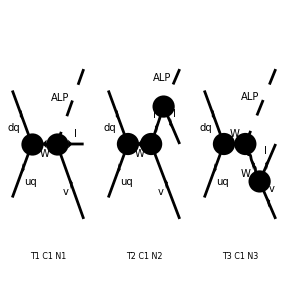

```mathematica
Paint[diag];
```

```mathematica
diag1 = DiagramExtract[diag, 1];
```

```mathematica
amp1=CreateFeynAmp[diag1]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

FAFeynAmpList(Process→(F(4,{Gen1,Col1}) | p1 | Md(Gen1,Col1) | {-Q/3}
-F(3,{Gen2,Col2}) | p2 | Mu(Gen2,Col2) | {-(2 Q)/3})→(S(105) | k1 | 0 | {}
F(2,{Gen4}) | k2 | Ml(Gen4) | {-Q,LeptonNumber}
-F(1,{Gen5}) | k3 | 0 | {-LeptonNumber}),Model→{ALP_leptophilic},GenericModel→{ALP_leptophilic},AmplitudeLevel→{Classes},ExcludeParticles→{S(2),-S(3),S(3)},ExcludeFieldPoints→{},LastSelections→{})(FAFeynAmp(GraphID(Topology==1,Generic==1,Classes==1,Number==1),Integral[],g(Lor1,Lor2) 1/((k1+k2+k3)^2-(FCGV(MW))^2) SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Gen1,3,External) SumOver(Gen2,3,External) SumOver(Gen4,3,External) SumOver(Gen5,3,External) ū(k2,Ml(Gen4)).(ⅈ gc81 IndexDelta(Gen4,Gen5) ga(Lor2).(omSubscript[-])).v(k3,0) v̄(p2,Mu(Gen2,Col2)).(ⅈ IndexDelta(Col1,Col2) gc87(Gen2,Gen1) ga(Lor1).(omSubscript[-])).u(p1,Md(Gen1,Col1))))

```mathematica
FCFAConvert[amp1, IncomingMomenta -> {pb, pu}, OutgoingMomenta->{pa, pl, pν}]
```

{((ḡ)^Lor1Lor2 SumOver(Col1,3,External) SumOver(Col2,3,External) SumOver(Gen1,3,External) SumOver(Gen2,3,External) SumOver(Gen4,3,External) SumOver(Gen5,3,External) (φ(OverBar[pl],Ml(Gen4))).(ⅈ gc81 (γ̄)^Lor2.(γ̄)^7 IndexDelta(Gen4,Gen5)).(φ(-OverBar[pν])) (φ(-OverBar[pu],Mu(Gen2,Col2))).(ⅈ (γ̄)^Lor1.(γ̄)^7 δ_Col1Col2 gc87(Gen2,Gen1)).(φ(OverBar[pb],Md(Gen1,Col1))))/((OverBar[pa]+OverBar[pl]+OverBar[pν])^2-(FCGV(MW))^2)}

```mathematica
A2 =DiracSimplify[FermionSpinSum[SpinorVBar[pl, ml].GS[pB].GA[7].SpinorU[pν, 0] SpinorUBar[pν,0].GA[6].GS[pB].SpinorV[pl, ml]]]/.{SP[pl, pl]->ml^2, SP[pa, pa]->ma^2, SP[pν, pν]->0}
```

-ma^2 mM^2+ml^2 mM^2-ml^2 t+s t

```mathematica
SP[pB, pl]=(mM^2+ml^2-s)/2
```

1/2 (ml^2+mM^2-s)

```mathematica
SP[pB, pν] = (mM^2-t)/2
```

1/2 (mM^2-t)

```mathematica
SP[pB, pB]=mM^2
```

mM^2

```mathematica
SP[pl, pl]=ml^2
```

ml^2

```mathematica
SP[pa, pa]=ma^2
```

ma^2

```mathematica
SP[pν, pν]=0
```

0

```mathematica
SP[pa, pν]=(s-ma^2)/2
```

1/2 (s-ma^2)

```mathematica
SP[pa, pl] = (t-ma^2-ml^2)/2
```

1/2 (-ma^2-ml^2+t)

```mathematica
SP[pl,pν]= (u-ml^2)/2
```

1/2 (ma^2+mM^2-s-t)

```mathematica
u = mM^2+ma^2+ml^2-s-t
```

ma^2+ml^2+mM^2-s-t

```mathematica
ma^2+2SP[pa, pl]
```

t-ml^2

```mathematica
A2
```

-ma^2 mM^2+ml^2 mM^2-ml^2 t+s t

```mathematica
E2s = (s+ma^2)/(2 √s)
```

(ma^2+s)/(2 √s)

```mathematica
E3s = (mM^2-s-ml^2)/(2 √s)
```

(-ml^2+mM^2-s)/(2 √s)

```mathematica
tmax = Simplify[(E2s+E3s)^2-(√(E2s^2-ma^2)-√(E3s^2-ml^2))^2]
```

(ma^2 (-ml^2+mM^2+s)+s (√(((ma^2-s)^2)/s) √((ml^4-2 ml^2 (mM^2+s)+(mM^2-s)^2)/s)+ml^2+mM^2-s))/(2 s)

```mathematica
tmin = Simplify[(E2s+E3s)^2-(√(E2s^2-ma^2)+√(E3s^2-ml^2))^2]
```

(ma^2 (-ml^2+mM^2+s)+s (-√(((ma^2-s)^2)/s) √((ml^4-2 ml^2 (mM^2+s)+(mM^2-s)^2)/s)+ml^2+mM^2-s))/(2 s)

```mathematica
Simplify[(A2/.t->tmin)/.s->ma^2]
```

0

```mathematica
Simplify[(A2/.t->tmax)/.s->ma^2]
```

0

```mathematica
Simplify[tmin/.s->ma^2, Assumptions->{ml>0, ma>0, mM>ml+ma}]
```

mM^2

```mathematica
Simplify[tmax/.s->ma^2, Assumptions->{ml>0, ma>0, mM>ml+ma}]
```

mM^2

```mathematica
Simplify[(A2/.t->tmin)/.s->(mM-ml)^2, Assumptions->{ml>0, ma>0, mM>ml+ma}]
```

-(ml mM^2 ((ml-mM)^2-ma^2))/(ml-mM)

```mathematica
Simplify[(A2/.t->tmax)/.s->(mM-ml)^2, Assumptions->{ml>0, ma>0, mM>ml+ma}]
```

-(ml mM^2 ((ml-mM)^2-ma^2))/(ml-mM)

```mathematica
tlim1=(mM^2 (-ma^2+2 ml^2+mM^2-s+√(ma^4+(mM^2-s)^2-2 ma^2 (mM^2+s))))/(-ma^2+mM^2+s+√(ma^4+(mM^2-s)^2-2 ma^2 (mM^2+s)))
```

(mM^2 (-ma^2+√(ma^4-2 ma^2 (mM^2+s)+(mM^2-s)^2)+2 ml^2+mM^2-s))/(-ma^2+√(ma^4-2 ma^2 (mM^2+s)+(mM^2-s)^2)+mM^2+s)

```mathematica
tlim2=(mM^2 (-ma^2+2 ml^2+mM^2-s-√(ma^4+(mM^2-s)^2-2 ma^2 (mM^2+s))))/(-ma^2+mM^2+s-√(ma^4+(mM^2-s)^2-2 ma^2 (mM^2+s)))
```

(mM^2 (-ma^2-√(ma^4-2 ma^2 (mM^2+s)+(mM^2-s)^2)+2 ml^2+mM^2-s))/(-ma^2-√(ma^4-2 ma^2 (mM^2+s)+(mM^2-s)^2)+mM^2+s)

```mathematica
Al = (Gf fM /(√2 fa))^2 Abs[Vckm]^2 A2/((2π)^3 32 mM^3)
```

1/(512 π^3 fa^2 mM^3)fM^2 Gf^2 Abs[Vckm]^2 (ml^2 (ma^2+mM^2-s-t)+(s-ma^2) (-ma^2-ml^2+t)+2 ml^2 (s-ma^2)-(ma^2 (ma^2+mM^2-s-t)))

```mathematica
Expand[Al]
```

-(8.56402×10^-15 fM^2 ma^2 Abs[Vckm]^2)/(fa^2 mM)-(8.56402×10^-15 fM^2 ml^2 t Abs[Vckm]^2)/(fa^2 mM^3)+(8.56402×10^-15 fM^2 ml^2 Abs[Vckm]^2)/(fa^2 mM)+(8.56402×10^-15 fM^2 s t Abs[Vckm]^2)/(fa^2 mM^3)

```mathematica
md=4.8 10^-3;
mu=2.3 10^-3;
ms=95 10^-3;
mc=1.275;
mt=170;
mb=4.4;
Cmu=0.3355;
Cmd=0.3395;
Cms=0.486;
Cmc=1.550;
Cmb=4.730;
mw=80.385;

me=0.51099895000*10^-3;
mμ=105.6583755*10^-3;
mτ=1776.86*10^-3;

MCC=3.0969;
MB=5.279;
MBc=6.274;
MBc2=6.871;
MD=1869.58*10^-3;
MDs=1968.47*10^-3;
MΥ1=9.46;
MΥ3=10.3552;
MB0=5.27955;
mks=0.89166;(*K STAR MASS*)
mk=0.497611;
Mπ=139.57061*10^-3;
mRhoplus=0.776
mPiplus=0.13957018; (*Pi+*)
mPi0=0.1349766;(*Pi0*)
mK0=0.497614; (*K0*)
mKplus=0.493677;(*K+*)
mKst=0.896;
mDs={1.96849,0.00032};(*Ds plus *)
mDplus=1.86962;
mDzero=1.86486;
mBplus=5.27925;
mBs=5.36689;
mBc=6.2751; 
mηc=2.9836;


(** DECAY CONSTANTS GeV**)

fπ=130.7*10^-3;
fρ=.223;
fk=155.8*10^-3;
fks=.217;
fB=189.9*10^-3;
fBs=0.225;
fJ=0.401
fD=211.9*10^-3; 
fBc=0.434;
fDs=0.249;
fΥT=0.659;
fΥ1=649*10^-3;
fΥ[2]=0.468;
fΥ[3]=539*10^-3;
fΥ[4]=0.349;

eps=1.6*10^-3;

(** CKM ENTRIES **)
VCKMw[λ_,ρ_,A_,η_]:={{1-λ^2/2-λ^4/8,λ,A*λ^3*(ρ-I η)},{-λ (1+A^2λ^4*(ρ+I* η-1/2)),1-λ^2/2-λ^4/8*(1+4*A^2),A*λ^2},
{A*λ^3(1-(ρ+I*η)(1-λ^2/2)),-A*λ^2(1+λ^2(ρ+I η-1/2)),1-A^2/2*λ^4}}

Vudw[{λ_,ρ_,A_,η_}]:=VCKMw[λ,ρ,A,η][[1,1]]
Vusw[{λ_,ρ_,A_,η_}]:=VCKMw[λ,ρ,A,η][[1,2]]
Vubw[{λ_,ρ_,A_,η_}]:=VCKMw[λ,ρ,A,η][[1,3]]

Vcdw[{λ_,ρ_,A_,η_}]:=VCKMw[λ,ρ,A,η][[2,1]]
Vcsw[{λ_,ρ_,A_,η_}]:=VCKMw[λ,ρ,A,η][[2,2]]
Vcbw[{λ_,ρ_,A_,η_}]:=VCKMw[λ,ρ,A,η][[2,3]]

Vtdw[{λ_,ρ_,A_,η_}]:=VCKMw[λ,ρ,A,η][[3,1]]
Vtsw[{λ_,ρ_,A_,η_}]:=VCKMw[λ,ρ,A,η][[3,2]]
Vtbw[{λ_,ρ_,A_,η_}]:=VCKMw[λ,ρ,A,η][[3,3]]

(* UTfit *)
λut={0.22534,0.00065};
ρut={0.132,0.023};
Aut={0.821,0.012};
ηut={0.352,0.014};

(* Central values *)
Vud=Vudw[{λut[[1]],ρut[[1]],Aut[[1]],ηut[[1]]}];
Vus=Vusw[{λut[[1]],ρut[[1]],Aut[[1]],ηut[[1]]}];
Vub=Vubw[{λut[[1]],ρut[[1]],Aut[[1]],ηut[[1]]}];
Vcd=Vcdw[{λut[[1]],ρut[[1]],Aut[[1]],ηut[[1]]}];
Vcs=Vcsw[{λut[[1]],ρut[[1]],Aut[[1]],ηut[[1]]}];
Vcb=Vcbw[{λut[[1]],ρut[[1]],Aut[[1]],ηut[[1]]}];
Vtd=Vtdw[{λut[[1]],ρut[[1]],Aut[[1]],ηut[[1]]}];
Vts=Vtsw[{λut[[1]],ρut[[1]],Aut[[1]],ηut[[1]]}];
Vtb=Vtbw[{λut[[1]],ρut[[1]],Aut[[1]],ηut[[1]]}];
```

0.776

0.401

```mathematica
Gf=1.166*10^-5;
αem=1/129;

(** DECAY WIDTHS/DECAY TIME & ρ  **)
tauKplus={1.2380 10^-8,0.0021 10^-8}/(6.582 10^-25);
tauKL={5.116 10^-8,0.021 10^-8}/(6.582 10^-25);
tauDplus={1.040,0.007}*10^-12/(6.582 10^-25);
tauDzero={4.101,0.015}*10^-13/(6.582 10^-25);
tauPiplus = {2.6033, 0.0005}*10^-8/(6.582 10^-25);
tauDs={5,0.07}10^-13/(6.582 10^-25);
tauBplus={1641,8}10^-15/(6.582 10^-25);
tauBzero={1.519,0.004}10^-12/(6.582 10^-25);
tauTau={2.906,0.010}10^-13/ (6.582 10^-25);
tauBc={0.507,0.009}10^-12/ (6.582 10^-25);
tauCC=(7.9*10^-21)/ (6.582 10^-25);

Γbs=1/(1.620*10^−12*(1.52*10^24));
Γb=1/(1.641*10^−12*(1.52*10^24));
ΓD=1/(1040*10^-15*(1.52*10^24));
ΓDs=1/((5.00)×10^-13*(1.52*10^24));
ΓΥ1=54.022*10^-6;
ΓΥ[2]=31.98*10^-6;
ΓΥ[3]=20.32*10^-6;
ΓΥ[4]=20.5*10^-3;
Γk=1/((1.2380*10^-8)*(1.52*10^24));
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
glBtoE=Table[{i,Re[NIntegrate[Simplify[(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fB,ml->me,cl->1,mM->MB,Vckm->Vub,mq1->Cmb,mq2->Cmu}]/Γb/.ma->i],t]/.t->tmax/.{ma->i,mM->MB,ml->me})-(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fB,ml->me,cl->1,mM->MB,Vckm->Vub,mq1->Cmb,mq2->Cmu}]/Γb/.ma->i],t]/.t->tmin/.{ma->i,mM->MB,ml->me})],{s,i^2,(MB-me)^2}]]},{i,0.001,MB-1.01*me,0.05}];
```

```mathematica
Export["EWVglBtoE.dat",glBtoE]
```

EWVglBtoE.dat

```mathematica
glBtoMu=Table[{i,Re[NIntegrate[Simplify[(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fB,ml->mμ,cl->1,mM->MB,Vckm->Vub,cq1->1,cq2->1,mq1->Cmb,mq2->Cmu}]/Γb/.ma->i],t]/.t->tmax/.{ma->i,mM->MB,ml->mμ})-(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fB,ml->mμ,cl->1,mM->MB,Vckm->Vub,cq1->1,cq2->1,mq1->Cmb,mq2->Cmu}]/Γb/.ma->i],t]/.t->tmin/.{ma->i,mM->MB,ml->mμ})],{s,i^2,(MB-mμ)^2}]]},{i,0.001,MB-1.01mμ,0.05}];
```

```mathematica
Export["EWVglBtoMu.dat",glBtoMu]
```

EWVglBtoMu.dat

```mathematica
glBtoTau=Table[{i,Re[NIntegrate[Simplify[(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fB,ml->mτ,cl->1,mM->MB,Vckm->Vub,cq1->1,cq2->1,mq1->Cmb,mq2->Cmu}]/Γb/.ma->i],t]/.t->tmax/.{ma->i,mM->MB,ml->mτ})-(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fB,ml->mτ,cl->1,mM->MB,Vckm->Vub,cq1->1,cq2->1,mq1->Cmb,mq2->Cmu}]/Γb/.ma->i],t]/.t->tmin/.{ma->i,mM->MB,ml->mτ})],{s,i^2,(MB-mτ)^2}]]},{i,0.001,MB-1.01mτ,0.05}];
```

```mathematica
Export["EWVglBtoTau.dat",glBtoTau]
```

EWVglBtoTau.dat

```mathematica
glDtoE=Table[{i,Re[NIntegrate[Simplify[(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fD,ml->me,cl->1,mM->MD,Vckm->Vcd,cq1->1,cq2->1,mq1->Cmd,mq2->Cmc}]/ΓD/.ma->i],t]/.t->tmax/.{ma->i,mM->MD,ml->me})-(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fD,ml->me,cl->1,mM->MD,Vckm->Vcd,cq1->1,cq2->1,mq1->Cmd,mq2->Cmc}]/ΓD/.ma->i],t]/.t->tmin/.{ma->i,mM->MD,ml->me})],{s,i^2,(MD-me)^2}]]},{i,0.001,MD-1.01me,0.05}];
```

```mathematica
Export["EWVglDtoE.dat",glDtoE]
```

EWVglDtoE.dat

```mathematica
glDtoMu=Table[{i,Re[NIntegrate[Simplify[(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fD,ml->mμ,cl->1,mM->MD,Vckm->Vcd,cq1->1,cq2->1,mq1->Cmd,mq2->Cmc}]/ΓD/.ma->i],t]/.t->tmax/.{ma->i,mM->MD,ml->mμ})-(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fD,ml->mμ,cl->1,mM->MD,Vckm->Vcd,cq1->1,cq2->1,mq1->Cmd,mq2->Cmc}]/ΓD/.ma->i],t]/.t->tmin/.{ma->i,mM->MD,ml->mμ})],{s,i^2,(MD-mμ)^2}]]},{i,0.001,MD-1.01mμ,0.05}];
```

```mathematica
Export["EWVglDtoMu.dat",glDtoMu]
```

EWVglDtoMu.dat

```mathematica
glDtoTau=Table[{i,Re[NIntegrate[Simplify[(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fD,ml->mτ,cl->1,mM->MD,Vckm->Vcd,cq1->1,cq2->1,mq1->Cmd,mq2->Cmc}]/ΓD/.ma->i],t]/.t->tmax/.{ma->i,mM->MD,ml->mτ})-(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fD,ml->mτ,cl->1,mM->MD,Vckm->Vcd,cq1->1,cq2->1,mq1->Cmd,mq2->Cmc}]/ΓD/.ma->i],t]/.t->tmin/.{ma->i,mM->MD,ml->mτ})],{s,i^2,(MD-mτ)^2}]]},{i,0.001,MD-1.01mτ,0.005}];
```

```mathematica
Export["EWVglDtoTau.dat",glDtoTau]
```

EWVglDtoTau.dat

```mathematica
glDstoE=Table[{i,Re[NIntegrate[Simplify[(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fDs,ml->me,cl->1,mM->MDs,Vckm->Vcs,cq1->1,cq2->1,mq1->Cms,mq2->Cmc}]/ΓDs/.ma->i],t]/.t->tmax/.{ma->i,mM->MDs,ml->me})-(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fDs,ml->me,cl->1,mM->MDs,Vckm->Vcs,cq1->1,cq2->1,mq1->Cms,mq2->Cmc}]/ΓDs/.ma->i],t]/.t->tmin/.{ma->i,mM->MDs,ml->me})],{s,i^2,(MDs-me)^2}]]},{i,0.001,MDs-1.01me,0.05}];
```

```mathematica
Export["EWVglDstoE.dat",glDstoE]
```

EWVglDstoE.dat

```mathematica
glDstoMu=Table[{i,Re[NIntegrate[Simplify[(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fDs,ml->mμ,cl->1,mM->MDs,Vckm->Vcs,cq1->1,cq2->1,mq1->Cms,mq2->Cmc}]/ΓDs/.ma->i],t]/.t->tmax/.{ma->i,mM->MDs,ml->mμ})-(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fDs,ml->mμ,cl->1,mM->MDs,Vckm->Vcs,cq1->1,cq2->1,mq1->Cms,mq2->Cmc}]/ΓDs/.ma->i],t]/.t->tmin/.{ma->i,mM->MDs,ml->mμ})],{s,i^2,(MDs-mμ)^2}]]},{i,0.001,MDs-1.01mμ,0.05}];
```

```mathematica
Export["EWVglDstoMu.dat",glDstoMu]
```

EWVglDstoMu.dat

```mathematica
glDstoTau=Table[{i,Re[NIntegrate[Simplify[(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fDs,ml->mτ,cl->1,mM->MDs,Vckm->Vcs,cq1->1,cq2->1,mq1->Cms,mq2->Cmc}]/ΓDs/.ma->i],t]/.t->tmax/.{ma->i,mM->MDs,ml->mτ})-(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fDs,ml->mτ,cl->1,mM->MDs,Vckm->Vcs,cq1->1,cq2->1,mq1->Cms,mq2->Cmc}]/ΓDs/.ma->i],t]/.t->tmin/.{ma->i,mM->MDs,ml->mτ})],{s,i^2,(MDs-mτ)^2}]]},{i,0.001,MDs-1.01mτ,0.005}];
```

```mathematica
Export["EWVglDstoTau.dat",glDstoTau]
```

EWVglDstoTau.dat

```mathematica
glKtoE=Table[{i,Re[NIntegrate[Simplify[(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fk,ml->me,cl->1,mM->mKplus,Vckm->Vus,mq1->Cms,mq2->Cmu}]*tauKplus[[1]]/.ma->i],t]/.t->tmax/.{ma->i,mM->mKplus,ml->me})-(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fk,ml->me,cl->1,mM->mKplus,Vckm->Vus,mq1->Cms,mq2->Cmu}]*tauKplus[[1]]/.ma->i],t]/.t->tmin/.{ma->i,mM->mKplus,ml->me})],{s,i^2,(mKplus-me)^2}]]},{i,0.001,mKplus-1.01me,0.01}];
```

```mathematica
Export["EWVglKtoE.dat",glKtoE]
```

EWVglKtoE.dat

```mathematica
glKtoMu=Table[{i,Re[NIntegrate[Simplify[(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fk,ml->mμ,cl->1,mM->mKplus,Vckm->Vus,cq1->1,cq2->1,mq1->Cms,mq2->Cmu}]*tauKplus[[1]]/.ma->i],t]/.t->tmax/.{ma->i,mM->mKplus,ml->mμ})-(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fk,ml->mμ,cl->1,mM->mKplus,Vckm->Vus,cq1->1,cq2->1,mq1->Cms,mq2->Cmu}]*tauKplus[[1]]/.ma->i],t]/.t->tmin/.{ma->i,mM->mKplus,ml->mμ})],{s,i^2,(mKplus-mμ)^2}]]},{i,0.001,mKplus-1.01mμ,0.01}];
```

```mathematica
Export["EWVglKtoMu.dat",glKtoMu]
```

EWVglKtoMu.dat

```mathematica
glπtoE=Table[{i,NIntegrate[Simplify[(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fπ,ml->me,cl->1,mM->mPiplus,Vckm->Vud,mq1->Cmd,mq2->Cmu}]*tauPiplus[[1]]/.ma->i],t]/.t->tmax/.{ma->i,mM->mPiplus,ml->me})-(Integrate[Simplify[Simplify[Al/.{fa->1000,fM->fπ,ml->me,cl->1,mM->mPiplus,Vckm->Vud,mq1->Cmd,mq2->Cmu}]*tauPiplus[[1]]/.ma->i],t]/.t->tmin/.{ma->i,mM->mPiplus,ml->me})],{s,i^2,(mPiplus-me)^2}]},{i,0.001,mPiplus-1.01me,0.001}];
```

```mathematica
Export["EWVglPitoE.dat",glπtoE]
```

EWVglPitoE.dat